# Lab 10: 3D Rotations and Interactive Controls

## Computer Graphics Lab, Wolfram Mathematica

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->True]
```

```mathematica
(* Question 1 *)
```

```mathematica
S[u_,v_]:={(v+2)*Cos[u],(v+2)*Sin[u],0.3*(u-v)}
```

```mathematica
objpara=ParametricPlot3D[S[u,v],{u,0,4*Pi},{v,0,6},Mesh->True,MeshStyle->Blue,PlotPoints->30,PlotStyle->{Orange,Specularity[5],Opacity[0.5]}]
```

-Graphics3D-

```mathematica
objgraphics=objpara[[1]];
```

```mathematica
anc={0,0,0};
```

```mathematica
objrotate[a_,b_]:=GeometricTransformation[objgraphics,Composition[TranslationTransform[anc],RotationTransform[a,{0,0,1}],RotationTransform[b,{1,0,0}]]]
```

```mathematica
colors=RandomColor[12]
```

{RGBColor[0.4004468698307344, 0.2581745757025933, 0.6701004819328289],RGBColor[0.595943190290811, 0.5055123400758572, 0.5396216993211556],RGBColor[0.7005247879873682, 0.6585335333252158, 0.1761106772840475],RGBColor[0.7983378835090127, 0.6796519241946841, 0.11392164298862029],RGBColor[0.09952970508241177, 0.30376185089458296, 0.29669138892140223],RGBColor[0.30740356366396404, 0.2255588015092902, 0.8242385418275455],RGBColor[0.22027555139942256, 0.7809436966097523, 0.37437112555357777],RGBColor[0.04526143377267822, 0.018421821300470098, 0.5745121042866028],RGBColor[0.21043254975653736, 0.4710870692227138, 0.37054366380974857],RGBColor[0.7779051387514844, 0.9717027820608404, 0.5919980672725458],RGBColor[0.278408432776607, 0.23481981071579194, 0.6164786827977189],RGBColor[0.739786882543433, 0.9255617165037651, 0.01871692715587825]}

```mathematica
Manipulate[Graphics3D[{objrotate[a,b],{c,Sphere[anc,1]}},PlotRange->10,Axes->True,AxesOrigin->{0,0,0}],{a,0,2*Pi},{b,0,2*Pi},{c,colors}]
```

```mathematica
(* Question 2 *)
```

```mathematica
obj1=Cube[1.6];
```

```mathematica
obj2=Dodecahedron[1];
```

```mathematica
obj3=ParametricPlot3D[{u,v,u*v},{u,-1,1},{v,-1,1}][[1]];
```

```mathematica
objlist={obj1->"Cube",obj2->"Dodecahedron",obj3->"Surface"};
```

```mathematica
rotatelist={{1,0,0}->"x-axis",{0,1,0}->"y-axis",{0,0,1}->"z-axis"};
```

```mathematica
objrotate2[o_,a_,ax_]:=GeometricTransformation[o,RotationTransform[a,ax]]
```

```mathematica
Graphics3D[objrotate2[obj3,Pi/3,{1,0,0}]];
```

```mathematica
Manipulate[Graphics3D[objrotate2[o,a,ax],PlotRange->2],{o,objlist,ControlType->PopupMenu},{ax,rotatelist,ControlType->PopupMenu},{a,0,2*Pi}]
```

```mathematica
(* Question 3 *)
```

```mathematica
tor=Torus[{0,0,0},{4,8}];
```

```mathematica
Graphics3D[{Red,tor}]
```

-Graphics3D-

```mathematica
Graphics3D[tor];
```

```mathematica
sph={Blue,Sphere[{0,0,0},1.3]};
```

```mathematica
Graphics3D[sph];
```

```mathematica
cen={Green,Icosahedron[{0,0,0}]};
```

```mathematica
Graphics3D[{Green,cen}];
```

```mathematica
rot1[a_]:=GeometricTransformation[sph,Composition[RotationTransform[a,{0,0,1}],TranslationTransform[{8,0,0}]]]
```

```mathematica
rot2[a_,b_,c_]:=GeometricTransformation[{{c,Opacity[0.8],tor},rot1[a]},RotationTransform[b,{0,1,0}]]
```

```mathematica
Manipulate[Graphics3D[{rot2[a,b,c],cen},PlotRange->12],{a,0,2*Pi},{b,0,2*Pi},{c,RandomColor[10]}]
```

```mathematica
(* Question 4 *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
menger=Import["Menger_sponge.stl","PolygonObjects"];
```

```mathematica
R=2;
```

```mathematica
Clear[cir]
```

```mathematica
cir[c_]:=ParametricPlot3D[{R*Sin[u],0,R*Cos[u]},{u,0,2*Pi},PlotStyle->{Thickness[0.05],c}]
```

```mathematica
colors4=ColorSlider[Dynamic[c4]]
```

$CellContext`c4

```mathematica
Clear[cirgraphics]
```

```mathematica
cirgraphics[c_]:=cir[c][[1]];
```

```mathematica
cirrotate[a_,c_]:=GeometricTransformation[cirgraphics[c],RotationTransform[a,{0,0,1}]]
```

```mathematica
{colors4,Manipulate[Dynamic[Graphics3D[{{LightBlue,Lighting->"Neutral",Opacity[0.5],menger},{Red,Sphere[{0,0,0},0.7]},cirrotate[a,c4]},PlotRange->2,Axes->True,AxesLabel->{"x","y","z"}]],{a,0,2Pi}]}
```

{$CellContext`c4,}

```mathematica
(* Question 5 *)
```

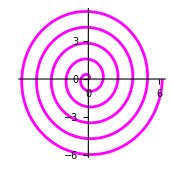

```mathematica
spr=ParametricPlot[{t*Cos[5*t],t*Sin[5*t]},{t,0,2*Pi},PlotStyle->Magenta]
```

```mathematica
sprgraphics={spr[[1]],{Blue,PointSize[0.05],Point[{0,0}]}};
```

```mathematica
xslide={Slider[Dynamic[x5],{-10,10},Background->Green],Dynamic[x5]};
```

```mathematica
yslide={Slider[Dynamic[y5],{-10,10},Background->Orange],Dynamic[y5]};
```

```mathematica
{xslide,yslide}
```

{{,},{,}}

```mathematica
pntgraphics=Dynamic[{PointSize[0.05],Red,Point[{x5,y5}]}];
```

```mathematica
Dynamic[Graphics[pntgraphics,PlotRange->11,Axes->True]];
```

```mathematica
sprrotate[a_]:=GeometricTransformation[sprgraphics,RotationTransform[a,{x5,y5}]]
```

```mathematica
{Manipulate[Dynamic[Graphics[{pntgraphics,sprrotate[a]},PlotRange->30,Axes->True,AxesOrigin->{0,0,0}]],{a,0,2*Pi}],xslide,yslide}
```

{,{,},{,}}

```mathematica
(* Question 6 *)
```

```mathematica
knot=ParametricPlot3D[{Sin[u]+2*Sin[2*u],Cos[u]-2*Cos[2*u],-Sin[3*u]},{u,0,2*Pi},PlotStyle->{Blue,Thickness[0.02]}]
```

-Graphics3D-

```mathematica
knotgraaphics=knot[[1]];
```

```mathematica
piece[k_]:=ParametricPlot3D[{Sin[u]+2*Sin[2*u],Cos[u]-2*Cos[2*u],-Sin[3*u]},{u,k,k+0.2},PlotStyle->{Red,Thickness[0.03]}]
```

```mathematica
piece[1];
```

```mathematica
knotall[k_]:=Show[knot,piece[k]]
```

```mathematica
Table[knotall[i],{i,1,10}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
knotgraphics[k_]:=knotall[k][[1]]
```

```mathematica
Manipulate[Graphics3D[{{Green,PointSize[0.03],Point[{0,0,0}]},GeometricTransformation[knotgraphics[t],RotationTransform[t,{0,0,1}]]},PlotRange->3,Axes->True],{t,0,2*Pi}]
```

```mathematica
pp[t_]:=GeometricTransformation[knotall[t],RotationTransform[t,{0,0,1}]]
```

```mathematica
Graphics3D[pp[1]]
```

-Graphics3D-